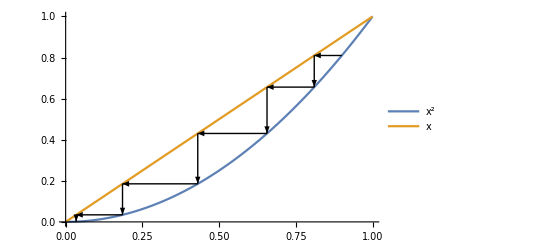

```mathematica
(*a[n+1]=a[n]^2*)
(*{x,f[x]}->{f[x],f[x]}->{f[x],f[f[x]]}*)
a0=0.9;
a={a0,f[a0]};
f[x_]=x^2;
fx[{x_,y_}]={y,y};
fy[{x_,y_}]={f[x],f[f[x]]};
first[b_]={Arrow[{b,fx[b]}],Arrow[{fx[b],fy[b]}]};(*封装一组箭头*)
list=NestList[fy[#]&,a,4];
Show[
Plot[{x^2,x},{x,0,1},PlotLegends->"Expressions"],
Graphics[{Arrowheads[0.02],
Flatten[first[#]&/@list]}
]]
```